```mathematica
f0 = Pi/6;k=1;d= 0.8; l = 1;ϵ =0.6; 
x1 = 0;x2 = 0;
RR:= k ϵ^-2 δ + ν ϵ^-1 dδ;
XX = (x1 - x2)/Cos[f0];
YY1 = y1/Sin[f0];YY2 = y2/Sin[f0];
μμ1 = μ1 Tan[f0];μμ2 = μ2 Tan[f0];
Φ[σ_,  μ1_, μ2_, Y1_, Y2_]:= 2 r + σ(μ1 Abs[r - Y1]- μ2 Abs[r + Y2] );
```

```mathematica
F[0] = Φ[1,  μμ1/.μ1->0.525, μμ2/.μ2->2.85, YY1/.y1->0.8, YY2/.y2->-2.4];
eqf0 = Cos[f0]^2(XX  - F[0]/.r->RR)/.ν->0/.ϵ->0.5
```

3/4 (-2 (0.+2.77778 δ)+1.64545 Abs[-4.8+2.77778 δ]-0.303109 Abs[-1.6+2.77778 δ])

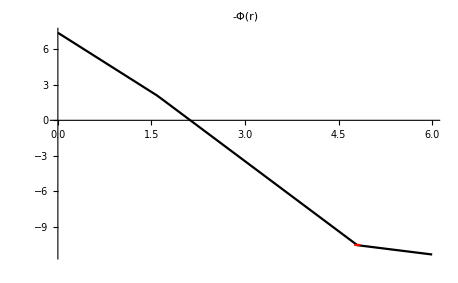

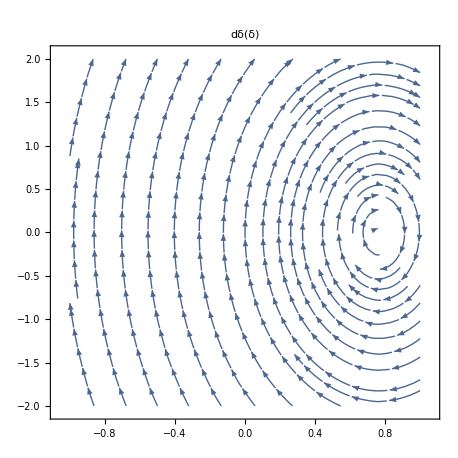

```mathematica
Show[Plot[- F[0],{r,0,6},PlotRange->All,PlotStyle->Black,PlotLabel->"-Φ(r)"],Plot[-10.55,{r,4.75,4.85},PlotStyle->Red]]
StreamPlot[{dδ, eqf0}, {δ,-1, 1},{dδ,-2, 2},StreamScale->{{0.1,0.1},Automatic},PlotLabel->"dδ(δ)"]
```

```mathematica
F[1] = Φ[ 1,0,0,3,2];
F[2] = Φ[ 1,0,5,3,2];
F[3] = Φ[1,-2,5,3,2];
F[4] = Φ[1,-7,4,3,2];
F[5] = Φ[1,-0.7,1,3,4];
F[6] = Φ[1,2,1,2,4];
F[7] = Φ[1,-3,4,3,-2];
F[8] = Φ[1,5,-7,3,-1];
F[9] = Φ[1,-2,-7,1,-2];
F[10] = Φ[1,2,3,2,-1];
F[11] = Φ[1,-5,-5,2,-1];
F[12] = Φ[1, -3,9,2,-1];
labels = {"-", "+", "++","-+","--","+-"};
labels =Join[labels,{"--+", "+--", "++-","-+-","---","-++","+-+","+++"}];
```

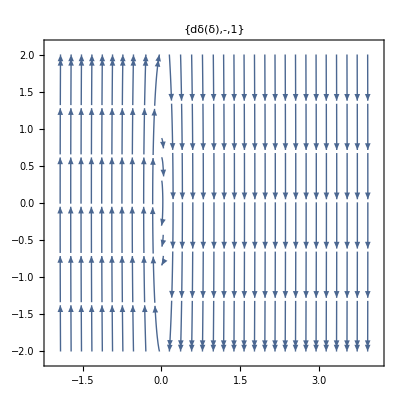
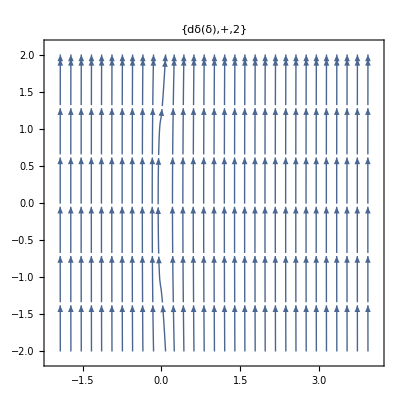
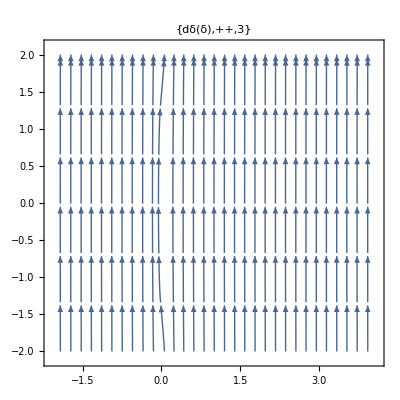
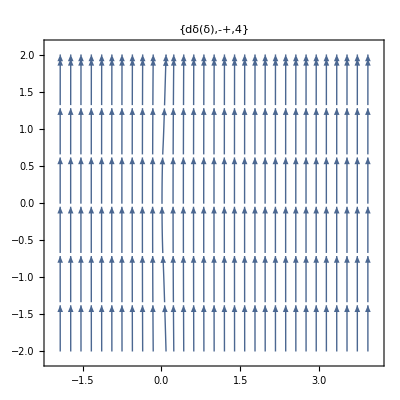
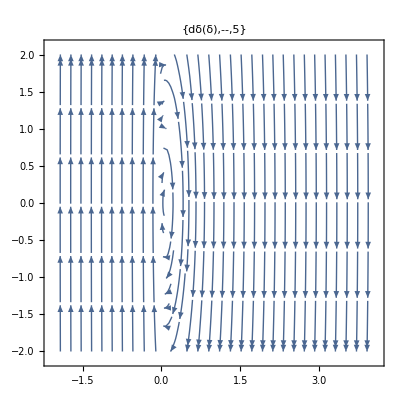
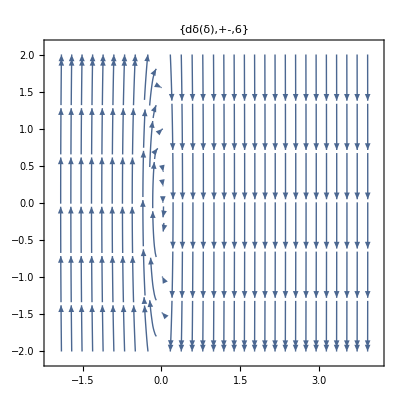
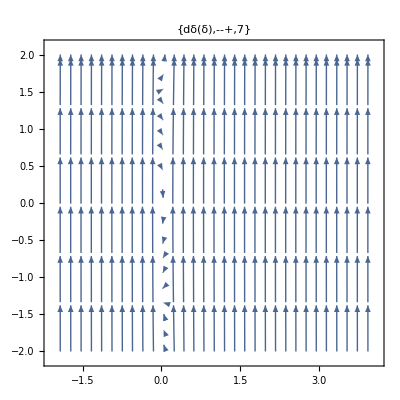
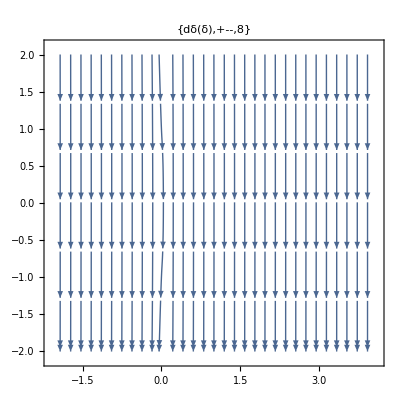

```mathematica
Table[
	StreamPlot[
         {dδ, Cos[f0]^2(XX  - F[i])/.r->RR/.ν->0/.ϵ->0.6}, 
	{δ,-2, 4},
	{dδ,-2, 2},
          StreamScale->{{0.1,0.1},Automatic},PlotLabel->{"dδ(δ)",labels[[i]] , i},
	PlotLabel->{"dδ(δ)",labels[[i]] , i}
	], 
	{i,1,12}
]
```

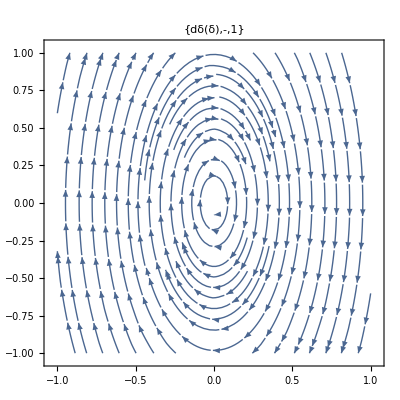
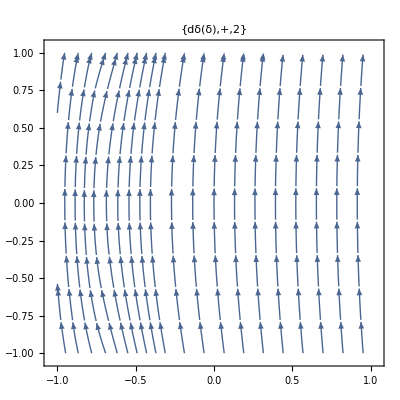
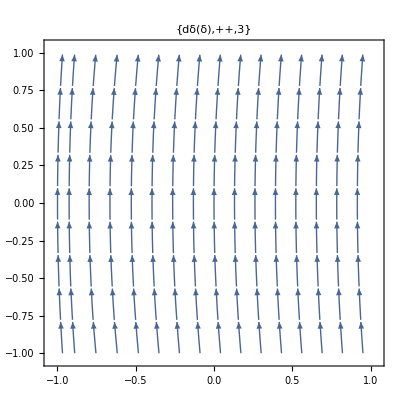
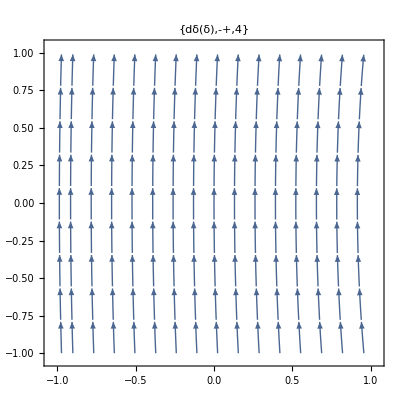
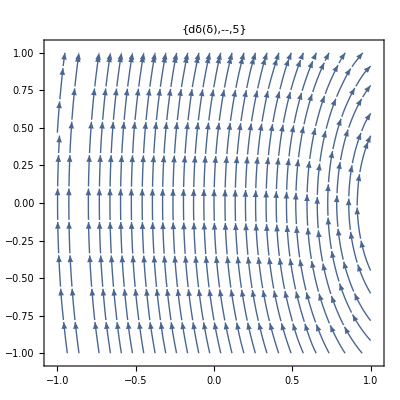
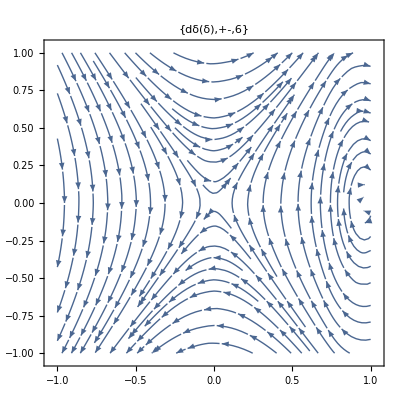
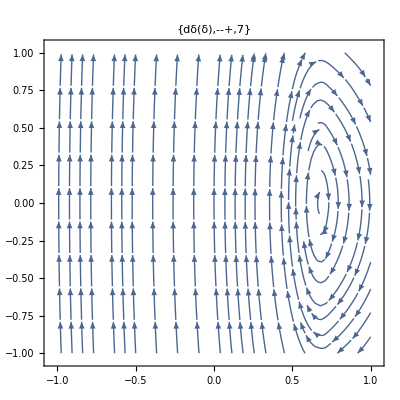
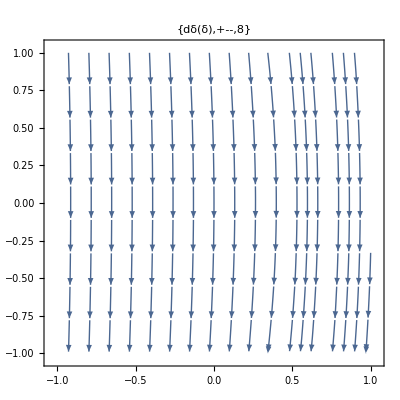

```mathematica
Table[
	StreamPlot[
         {dδ, Cos[f0]^2(XX  - F[i])/.r->RR/.ν->0/.ϵ->0.1}, 
	{δ,-1, 1},
	{dδ,-1, 1},
          StreamScale->{{0.1,0.1},Automatic},PlotLabel->{"dδ(δ)",labels[[i]] , i},
	PlotLabel->{"dδ(δ)",labels[[i]] , i}
	], 
	{i,1,12}
]
```

```mathematica
Manipulate[
	Table[
		StreamPlot[
		 {dδ, (Cos[f0]^2(XX  - F[i])/.r->RR/.ν->νν/.ϵ->0.6)}, 
		{δ,-2, 4},
		{dδ,-2, 2},
		StreamScale->{{0.1,0.1},Automatic},PlotLabel->{"dδ(δ)",labels[[i]] , i}
		],
		 {i,1,12}
	],{νν, -2, 2}
]
```

```mathematica
splot1 = StreamPlot[{dδ, Cos[f0]^2(XX  - F[6])/.r->RR},{δ,-4,4},{dδ,-3,3}];
eqf1 = Cos[f0]^2(XX  - F[0])/.r->RR/.δ->δ[t]/.dδ->dδ[t]/.ν->1
Manipulate[Show[splot1,
ParametricPlot[Evaluate[First[{δ[t],dδ[t]} /. NDSolve[{δ'[t]==dδ[t],dδ'[t]==eqf1,Thread[{δ[0],dδ[0]}==point]},{δ,dδ},{t,0,T}]]],{t,0,T},PlotStyle->Red]],
{{T,10},1,100},{{point,{1,0}},Locator}, SaveDefinitions->True]
```

3/4 (1.64545 Abs[-4.8+1.66667 dδ[t]+2.77778 δ[t]]-0.303109 Abs[-1.6+1.66667 dδ[t]+2.77778 δ[t]]-2 (1.66667 dδ[t]+2.77778 δ[t]))